# Medição tensão interfacial

## Solução da Equação de Bashforth e Addams

## Parâmetros físicos e geométricos

```mathematica
(*β=((Subscript[ρ, 1]-Subscript[ρ, 2])gb^2)/γ*)
b=2.3968253968253967;                                        (*Raio do apice*)
P=15.046/(2*b);                                           (*Comprimento do contorno divido por b e por 2*)
Dia=0.995;
h=5.715;                                            (*distância entre o apice e a parte superior da gota*)
(*Vd= 30;*)                                              (*Volume da gota*)

reso=1/63;                                           (*Quantidade de pixels em 1 mm*)
Unidade={"Pars","g[m/s^2]=","b[mm] =","ρ_1[m^3/kg]=","ρ_2[m^3/kg]=","β[mN/m] =","Vd[uL] =","D[mm] ="};Valor={"Valor",g=9.81,b,ρ1=870,ρ2=1000,"-",Vd,Dia};
MatrixForm[Table[{Unidade[[i]],Valor[[i]]},{i,Length[Unidade]}]]
```

(Pars | Valor
g[m/s^2]= | 9.81
b[mm] = | 2.39683
ρ_1[m^3/kg]= | 870
ρ_2[m^3/kg]= | 1000
β[mN/m] = | -
Vd[uL] = | Vd
D[mm] = | 0.995)

## Extração contorno de Imagem

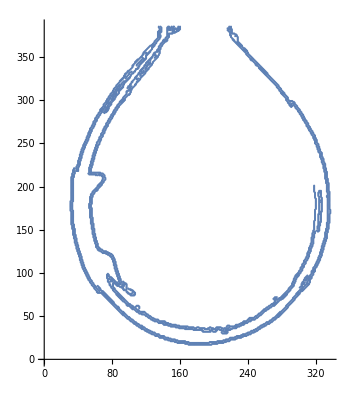

```mathematica
ImA0=-Graphics-;
 BrightnessEqualize[ImA0] ;
 ColorNegate[ImA0];
ImA0=MorphologicalBinarize[ImA0];
Manipulate[ImageSubtract[ImA0,a],{{a,0.1},0,1}];
ImA1 = ImageSubtract[ImA0,0.3];
Manipulate[LaplacianGaussianFilter[ImA1,b],{{b,1},0.5,3}];
ImA2 = LaplacianGaussianFilter[ImA1,1.4];
Manipulate[ContourDetect[ImA3,a],{{a,0.5},0,1}];
ImA3= ContourDetect[ImA2,0.205];
Manipulate[EdgeDetect[ImA3,r,t],{{r,2,"radius"},0,20},{{t,.1,"threshold"},0,.5}];
ImA4=EdgeDetect[ImA3,2,0.402];
list =ImageValuePositions[ImA4,White];
GExp=PixelValuePositions[ImA4,White];
GExpp=Sort[GExp,#1[[1]]<#2[[1]]&];
reso(-GExpp[[1]][[1]]+GExpp[[-1]][[1]])/2//N;
(*n=Round[(+GExpp[[1]][[1]]+GExpp[[-1]][[1]])/2]*)
(*n=Round[Mean[Table[GExp[[i]][[1]],{i,1,Length[GExp]}]]]//N*)

n=Mean[{GExpp[[1]][[1]],GExpp[[-1]][[1]]}];

GExpFig=ListPlot[GExp,AspectRatio->Automatic]
```

## Definindo equação

```mathematica
(*Chute Inicial para β*)
k=1.392*Pi*10^-3;
betaini=-√Exp[-6.70905+15.30025k-16.44709 k^2+9.92425 k^3-2.585035 k^4];
(*Função teorica*)
GTeo[β_]:=NDSolve[{D[Fi[s],s]==β*z[s]+2-(Sin[Fi[s]]/x[s]),Cos[Fi[s]]==D[x[s],s],Sin[Fi[s]]==D[z[s],s],x[0]==1 10^-8,z[0]==0,Fi[0]==0},{x,z},{s,P}];
GTeoFig[β_,b_]:=ParametricPlot[Evaluate[b*{-x[s],z[s]}/. GTeo[β]],{s,0,P},AspectRatio->Automatic,PlotStyle->Green];
GTeoFigPos[β_,b_]:=ParametricPlot[Evaluate[b*{x[s],z[s]}/. GTeo[β]],{s,0,P},AspectRatio->Automatic,PlotStyle->Green];
```

```mathematica
(*Tratamento dos dados experimentais 1*)
(*n é ponto x que divide a gota simetricamente*)
(*reso é conversão de pixel para SI*)
TratI[GExp0_]:=
Module[{GExp=GExp0,GExp2,yminor,xmax,count},
count=0;
Do[If[GExp[[i]][[1]]≤n,count=count+1],{i,Length[GExp]}];

GExp2 =Table[If[GExp[[i]][[1]]≤n,GExp[[i]],{}],{i,Length[GExp]}];
GExp2=DeleteCases[GExp2,{}];
 Do[If[GExp2[[i+1]][[2]]<=GExp2[[i]][[2]],yminor=GExp2[[i+1]][[2]]],{i,2,Length[GExp2]-1}];
 Do[If[GExp2[[i+1]][[1]]>=GExp2[[i]][[1]],xmax=GExp2[[i+1]][[1]]],{i,2,Length[GExp2]-1}];
GExp2 = reso*Table[{GExp2[[i]][[1]]-xmax,GExp2[[i]][[2]]-yminor},{i,Length[GExp2]}];
GExp2=Sort[GExp2,#1[[2]]<#2[[2]]&];
GExp2=Table[If[GExp2[[i]][[2]]<h,GExp2[[i]],Nothing],{i,1,Length[GExp2]}];

GExp2
]
```

```mathematica
TratI[GExp]//N;
```

```mathematica
(*Segunda função para tratamento dos dados*)

TratII[GExp20_]:=
Module[{GExp2=GExp20,count1,CordZ,CordX,CordZ2,CordX2,CordZ3,GExp3},
CordZ=Table[GExp2[[i]][[2]],{i,Length[GExp2]}];
CordX=Table[GExp2[[i]][[1]],{i,Length[GExp2]}];
CordZ2=Split[CordZ];
count1=Table[Length[CordZ2[[i]]],{i,1,Length[CordZ2]}];
CordX2=TakeList[CordX,count1];
CordZ3= Table[CordZ2[[i]][[1]],{i,1,Length[CordZ2]}];
CordX3=Table[Min[CordX2[[i]]],{i,1,Length[CordX2]}];
Length[CordX3]==Length[CordZ3];
GExp3=Table[{CordX3[[i]],CordZ3[[i]]},{i,1,Length[CordZ3]}];
GExp3Fig=ListPlot[GExp3,AspectRatio->Automatic];
GExp3
]
```

```mathematica
TratII[TratI[GExp]]//N;
```

```mathematica
(*Terceira função, CRIAÇÃO DA CURVA TEORICA*)
Xteo[β0_,b_]:=
Module[{β=β0,xx,zz,GExp3,zzExp,zzTeo,xzTeo,lista,sPara,xxExp},
GExp3=TratII[TratI[GExp]];
xx[s] =( x[s]/.GTeo[β]);
zz[s]=(z[s]/.GTeo[β]);
xxExp={};
zzExp={};
xxExp= Table[GExp3[[i,1]],{i,Length[GExp3]}]/b   ;
zzExp= Table[GExp3[[i,2]],{i,Length[GExp3]}]/b;
lista=Table[Solve[zz[s]==zzExp[[i]],s],{i,Length[zzExp]}];
lista=Flatten[lista,2];
lista=Table[If[Values[lista[[i]]]>P,lista[[i]]=s->P,lista[[i]]],{i,1,Length[lista]}];
sPara=Table[lista[[i]][[2]],{i,1,Length[lista]}];
Flatten[Evaluate[-xx[s]/.s->sPara]];
Flatten[Evaluate[zz[s]/.s->sPara]];

xxTeo=b*Flatten[Evaluate[-xx[s]/.s->sPara]];
xxTeo=Table[If[xxTeo[[i]]>-10^-6,xxTeo[[i]]=0,xxTeo[[i]]],{i,1,Length[xxTeo]}];
zzTeo=b*Flatten[Evaluate[zz[s]/.s->sPara]];
xzTeo=Table[{xxTeo[[i]],zzTeo[[i]]},{i,Length[xxTeo]}];
xzTeoFig=ListPlot[xzTeo,AspectRatio->Automatic,PlotStyle->Red];
xxTeo
]
```

## Relação curva teórica e experimental para x positivo

```mathematica
TratIPos[GExp0_]:=
Module[{GExp=GExp0,GExp2,yminor,xmax,count=0,Menorx},
Do[If[GExp[[i]][[1]]>n,count=count+1],{i,Length[GExp]}];

GExp2 =Table[If[GExp[[i]][[1]]>n,GExp[[i]],{}],{i,Length[GExp]}];
GExp2=DeleteCases[GExp2,{}];
Menorx=Min[Table[GExp2[[i]][[1]],{i,1,Length[GExp2]}]];
 Do[If[GExp2[[i+1]][[2]]<=GExp2[[i]][[2]],yminor=GExp2[[i+1]][[2]]],{i,2,Length[GExp2]-1}];
 Do[If[GExp2[[i+1]][[1]]>=GExp2[[i]][[1]],xmax=GExp2[[i+1]][[1]]],{i,2,Length[GExp2]-1}];
GExp2 = reso*Table[{GExp2[[i]][[1]]-Menorx,GExp2[[i]][[2]]-yminor},{i,Length[GExp2]}];
GExp2=Sort[GExp2,#1[[2]]<#2[[2]]&];
GExp2=Table[If[GExp2[[i]][[2]]<h,GExp2[[i]],Nothing],{i,1,Length[GExp2]}];

GExp2
]
```

```mathematica
TratIPos[GExp]//N;
```

```mathematica
TratIIPos[GExp20_]:=
Module[{GExp2=GExp20,count1,CordZ,CordX,CordZ2,CordX2,CordZ3,GExp3},
CordZ=Table[GExp2[[i]][[2]],{i,Length[GExp2]}];
CordX=Table[GExp2[[i]][[1]],{i,Length[GExp2]}];
CordZ2=Split[CordZ];
count1=Table[Length[CordZ2[[i]]],{i,1,Length[CordZ2]}];
CordX2=TakeList[CordX,count1];
CordZ3= Table[CordZ2[[i]][[1]],{i,1,Length[CordZ2]}];
CordX3Pos=Table[Max[CordX2[[i]]],{i,1,Length[CordX2]}];
Length[CordX3Pos]==Length[CordZ3];
GExp3=Table[{CordX3Pos[[i]],CordZ3[[i]]},{i,1,Length[CordZ3]}];
GExp3FigPos=ListPlot[GExp3,AspectRatio->Automatic];
GExp3
]
```

```mathematica
TratIIPos[TratIPos[GExp]]//N;
```

```mathematica
(*Terceira função, CRIAÇÃO DA CURVA TEORICA*)
XteoPos[β0_,b_]:=
Module[{β=β0,xx,zz,GExp3,zzExp,zzTeo,xzTeo,lista,sPara,xxExp},
GExp3=TratIIPos[TratIPos[GExp]];
xx[s] =( x[s]/.GTeo[β]);
zz[s]=(z[s]/.GTeo[β]);
xxExp={};
zzExp={};
xxExp= Table[GExp3[[i,1]],{i,Length[GExp3]}]/b   ;
zzExp= Table[GExp3[[i,2]],{i,Length[GExp3]}]/b;
lista=Table[Solve[zz[s]==zzExp[[i]],s],{i,Length[zzExp]}];
lista=Flatten[lista,2];
lista=Table[If[Values[lista[[i]]]>P,lista[[i]]=s->P,lista[[i]]],{i,1,Length[lista]}];
sPara=Table[lista[[i]][[2]],{i,1,Length[lista]}];
Flatten[Evaluate[xx[s]/.s->sPara]];
Flatten[Evaluate[zz[s]/.s->sPara]];

xxTeoPos=b*Flatten[Evaluate[xx[s]/.s->sPara]];
xxTeoPos=Table[If[xxTeoPos[[i]]<10^-6,xxTeoPos[[i]]=0,xxTeoPos[[i]]],{i,1,Length[xxTeoPos]}];
zzTeo=b*Flatten[Evaluate[zz[s]/.s->sPara]];
xzTeo=Table[{xxTeoPos[[i]],zzTeo[[i]]},{i,Length[xxTeoPos]}];
xzTeoFigPos=ListPlot[xzTeo,AspectRatio->Automatic,PlotStyle->Red];
xxTeoPos
]
```

## Funções objetivos

```mathematica
(*Função objetivo que usa todos os dados experimentais*)
FObjt1[xexp0_,xteo0_]:=Module[{Soma=0 ,xteo=xteo0,xexp=xexp0},
Do[Soma=(Soma+Sqrt[(xexp[[i]]-xteo[[i]])^2]),{i,1,Length[xexp]}];Soma]
```

```mathematica
(*Função objetivo que não usa os dados das coordenadas centrais  *)
FObjt2[xexp0_,xteo0_]:=Module[{Soma=0 ,xteo=xteo0,xexp=xexp0,divi},
divi=Round[Length[xexp]/3 ];
xteo=Delete[Partition[xteo,UpTo[divi]],2];
xexp=Delete[Partition[xexp,UpTo[divi]],2];
xteo=Flatten[xteo];
xexp=Flatten[xexp];

Do[Soma=(Soma+Sqrt[(xexp[[i]]-xteo[[i]])^2]),{i,1,Length[xexp]}];Soma]
```

```mathematica
ErroRel[ini0_,fin0_]:=Module[{fin=fin0,ini=ini0},Abs[fin-ini]/ini 100]
```

## Função que encontra o melhor Beta

```mathematica
TI[b_]:=Module[{listad,listaa,ini,fin,listad2},
Xteo[betaini];
XteoPos[betaini];
listad={betaini,-0.3};
ini= listad[[1]];
fin=listad[[2]];
Do[{ini= listad[[1]];
fin=listad[[2]];
listaa=Table[{(FObjt1[CordX3,Xteo[i,b]]+FObjt1[CordX3Pos,XteoPos[i,b]]),i},{i,ini,fin,-j}];
listab= Table[listaa[[i]][[1]],{i,1,Length[listaa]}];
listac= Table[listaa[[i]][[2]],{i,1,Length[listaa]}];
pos=Flatten[Position[listab,Min[listab]],2][[1]];
betinha= listac[[pos]];
If[j==0.05,listad2={betinha+j,betinha-j}];
listad={betinha+j,betinha-j}},{j,{0.05}}];
Do[{ini= listad[[1]];
fin=listad[[2]];
listaa=Table[{(FObjt1[CordX3,Xteo[i,b]]+FObjt1[CordX3Pos,XteoPos[i,b]]),i},{i,ini,fin,-j}];
listab= Table[listaa[[i]][[1]],{i,1,Length[listaa]}];
listac= Table[listaa[[i]][[2]],{i,1,Length[listaa]}];
pos=Flatten[Position[listab,Min[listab]],2][[1]];
betinha= listac[[pos]];
If[j==0.05,listad2={betinha+j,betinha-j}];
listad={betinha+j,betinha-j}},{j,{0.001}}];

xxx= betinha;

 γ=((ρ1-ρ2)g (b 10^-3)^2)/betinha 1000;
Wo = (-(ρ1-ρ2) g Vd 10^-9)/(Pi γ Dia 10^-6);
 γ
]
```

```mathematica
TI[b](*1.2686675753513614*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

48.165

```mathematica
(*Wo;*)
(*ErroRel[Wo,1];*)
xxx
γ
TimeUsed[]
```

-0.152108

48.165

148.559

## Figuras

### Parte Negativa

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

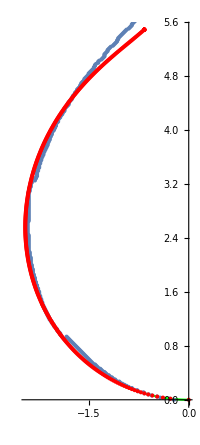

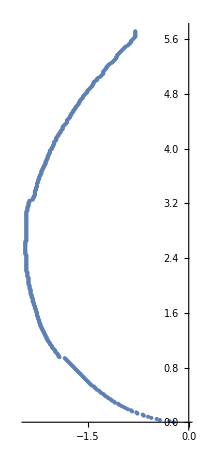
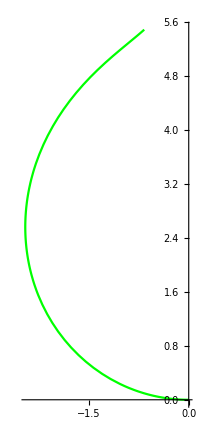
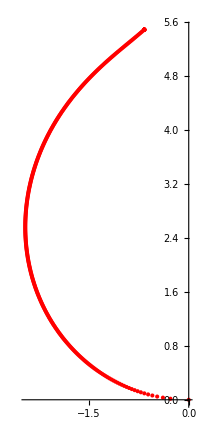

```mathematica
Xteo[xxx,b];
CordX3//N;
Show[GTeoFig[xxx,b],GExp3Fig,xzTeoFig,AspectRatio->Automatic]
{GExp3Fig,GTeoFig[xxx,b],xzTeoFig}
```

#### Parte Positiva e as duas partes juntas

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

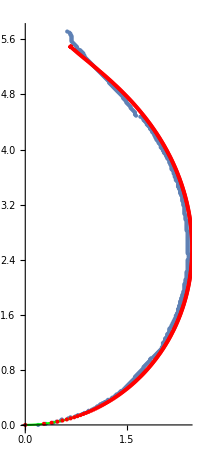

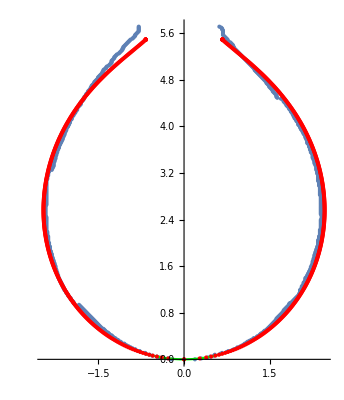

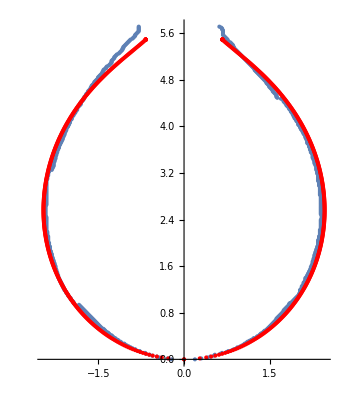

Show::gcomb: Could not combine the graphics objects in Show[GTeoFig[-0.3],GTeoFigPos[-0.3],PlotRange→Automatic,PlotLabel→Curva Teórica].

```mathematica
XteoPos[xxx,b];
Xteo[xxx,b];
CordX3Pos//N;

Length[lista];
Length[xxTeo];
Length[CordX3];
Show[GExp3FigPos,GTeoFigPos[xxx,b],xzTeoFigPos,AspectRatio->Automatic]
{GExp3FigPos,GTeoFigPos[xxx,b],xzTeoFigPos};
Show[GExp3FigPos,GTeoFigPos[xxx,b],xzTeoFigPos,GExp3Fig,GTeoFig[xxx,b],xzTeoFig,PlotRange->Automatic]
Show[GExp3FigPos,xzTeoFigPos,GExp3Fig,xzTeoFig,PlotRange->Automatic,PlotLegends->{"Curva Teorica","Curva Experimental"}]
Show[GTeoFig[-0.3],GTeoFigPos[-0.3],PlotRange->Automatic,PlotLabel->"Curva Teórica"];
```

## Parâmetros que mede a qualidade da medição - Wo

```mathematica
(*Wo ~ 1 - A tensão interfacial possui acuracia
Wo << 1 - A tensão interfacial não é confiável*)
```

```mathematica
Wo = ((Subscript[ρ, 1]-Subscript[ρ, 2]) g Vd)/(Pi γ D)
```

(0.0648317 Vd (ρ_1-ρ_2))/D

```mathematica
CordZ3
```

CordZ3

```mathematica
{2.824279041844041}
```

{2.82428}

```mathematica
{(12+4),12}
```

{16,12}

```mathematica
0
```

0

```mathematica
γ=((ρ1-ρ2)g (b 10^-3)^2)/-0.235 1000
```

31.1758

## Análise de resultados

```mathematica
permissao=0;
If[permissao==0,listaγ={}];
AppendTo[listaγ,γ];
```

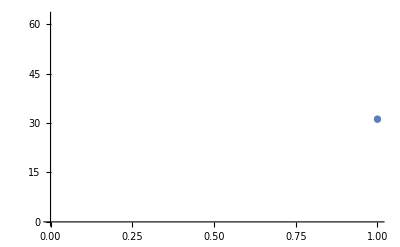

{31.1758}

```mathematica
ListPlot[listaγ]
listaγ
```

```mathematica
listaγ
```

{31.1758}

{{2.4127,5},{2.39683,32},{2.38095,17},{2.36508,9},{2.34921,15},{2.33333,7},{2.31746,8},{2.30159,5},{2.28571,8},{2.26984,5},{2.25397,9},{2.2381,3},{2.22222,6},{2.20635,5},{2.19048,5},{2.1746,3},{2.15873,6},{2.14286,3},{2.12698,7},{2.11111,2},{2.09524,5},{2.07937,3},{2.06349,4},{2.04762,3},{2.03175,6},{2.01587,3},{2.,4},{1.98413,2},{1.96825,3},{1.95238,2},{1.93651,3},{1.92063,3},{1.90476,3},{1.88889,2},{1.87302,2},{1.85714,2},{1.84127,4},{1.8254,2},{1.80952,2},{1.79365,3},{1.77778,2},{1.7619,2},{1.74603,4},{1.73016,2},{1.71429,1},{1.69841,2},{1.68254,1},{1.66667,1},{1.65079,1},{1.63492,2},{1.61905,5},{1.60317,2},{1.5873,2},{1.57143,2},{1.55556,3},{1.53968,2},{1.52381,2},{1.50794,2},{1.49206,3},{1.47619,2},{1.46032,2},{1.44444,3},{1.42857,1},{1.4127,2},{1.39683,2},{1.38095,2},{1.36508,1},{1.34921,2},{1.33333,2},{1.31746,2},{1.30159,1},{1.28571,2},{1.26984,2},{1.25397,1},{1.2381,2},{1.22222,2},{1.20635,2},{1.19048,1},{1.1746,2},{1.15873,1},{1.14286,2},{1.12698,1},{1.11111,2},{1.09524,2},{1.07937,1},{1.06349,2},{1.04762,2},{1.03175,1},{1.01587,2},{1.,1},{0.984127,2},{0.968254,1},{0.952381,1},{0.936508,2},{0.920635,2},{0.904762,1},{0.888889,1},{0.873016,3},{0.857143,2},{0.84127,2},{0.825397,1},{0.809524,1},{0.777778,2},{0.761905,2},{0.746032,2},{0.730159,1},{0.714286,1},{0.698413,1},{0.68254,6},{0.666667,3},{0.650794,1},{0.634921,1},{0.619048,1},{0.539683,1},{0.52381,1},{0.460317,1},{0.412698,1},{0.301587,1},{0.190476,1}}

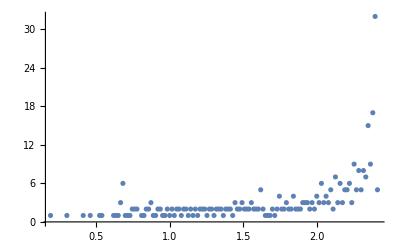

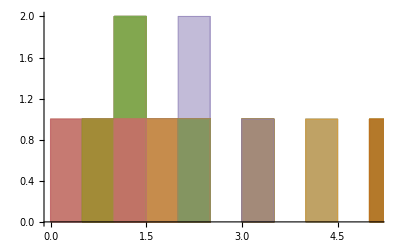

```mathematica
Sort[TratIIPos[TratIPos[GExp]],#1[[1]]>#2[[1]]&][[1]][[2]] //N;
A =Sort[TratIIPos[TratIPos[GExp]],#1[[1]]>#2[[1]]&] //N;
A1=Table[A[[i]][[1]],{i,Length[A]}];
A2=Split[A1];
A3=Table[{A2[[i]][[1]],Length[A2[[i]]]},{i,Length[A2]}]

ListPlot[A3,PlotRange->All]
Histogram[A3]
```

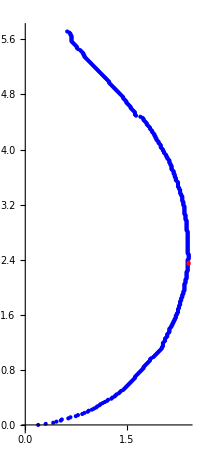

```mathematica
ListPlot[{TratIIPos[TratIPos[GExp]],{{2.4107142857142856,2.3392857142857144},{2.4107142857142856,2.357142857142857}}}, AspectRatio->Automatic,PlotStyle->{Blue,Red}]
```

```mathematica
Sort[TratII[TratI[GExp]],#1[[2]]<#2[[2]]&][[1]][[2]] //N;
Sort[TratII[TratI[GExp]],#1[[2]]<#2[[2]]&] //N;
```

```mathematica
ListPlot[TratII[TratI[GExp]], AspectRatio->Automatic]
```

-Graphics-

## Análise da estabilidade

CondTI[ϵ_]:= Norm[((TI[b(1+ϵ)]-TI[b])/TI[b])/(ϵ/b)]
CondTI[10^-5]
TimeUsed[]